silicon, cramped or free  @ both ends
b vs Q^-1 (L=10 um)

300K

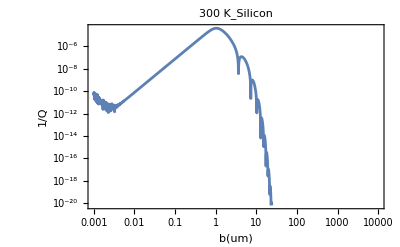

```mathematica
Qb300=Abs[3/(4 ξ^3)-ΔE/(Cos[2 d ξ]+Cosh[2 d ξ])(Cos[ξ(d-1)]Sinh[ξ(d+1)]+Cos[ξ(d+1)]Sinh[ξ(1-d)]-Sin[ξ(d-1)]Cosh[ξ(1+d)]+Sin[ξ(1+d)]Cosh[ξ(1-d)]-2ξ(Cos[ξ(d-1)]Cosh[ξ(1+d)]+Cos[ξ(d+1)]Cosh[ξ(1-d)]))]/.
{ξ->an/(4 3^(1/4))b^(3/2)/(L √lT)}/.
{d->1.3,lT->1.257 10^-2,an->4.73,ΔE->7.942 10^-5,L->10};

Qb300g=LogLogPlot[Qb300,{b,0.001,10000},PlotLabel->300K_Silicon, Frame->True,FrameLabel->{b[um],Q^-1}]
```

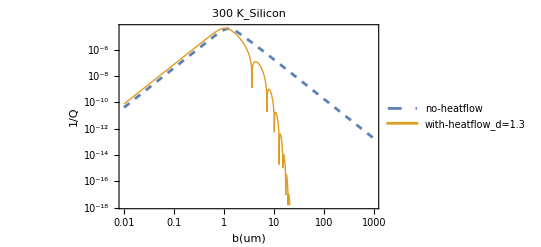

```mathematica
QNob300 =Abs[ ΔE(6/(2ξ)^2-6/(2ξ)^3(Sinh[2ξ]+Sin[2ξ])/(Cosh[2ξ]+Cos[2ξ]) )]/.
{ξ->an/(4 3^(1/4))b^(3/2)/(L √lT)}/.
{d->1.3,lT->1.257 10^-2,an->4.73,ΔE->7.942 10^-5,L->10};
Qb300g=LogLogPlot[{QNob300,Qb300},{b,0.01,1000},PlotLabel->300K_Silicon, PlotStyle->{Dashed,Thick},PlotLegends->Placed[{"no-heatflow","with-heatflow_d=1.3"},{0.3,0.25}],Frame->True,FrameLabel->{b[um],Q^-1}]
```

100K

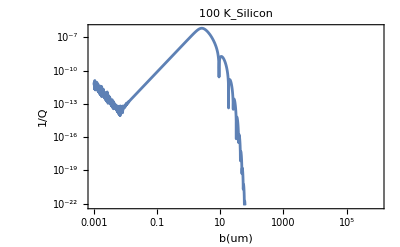

```mathematica
Qb100=Abs[3/(4 ξ^3)-ΔE/(Cos[2 d ξ]+Cosh[2 d ξ])(Cos[ξ(d-1)]Sinh[ξ(d+1)]+Cos[ξ(d+1)]Sinh[ξ(1-d)]-Sin[ξ(d-1)]Cosh[ξ(1+d)]+Sin[ξ(1+d)]Cosh[ξ(1-d)]-2ξ(Cos[ξ(d-1)]Cosh[ξ(1+d)]+Cos[ξ(d+1)]Cosh[ξ(1-d)]))]/.
{ξ->an/(4 3^(1/4))b^(3/2)/(L √lT)}/.
{d->1.3,lT->2.017 10^-1,an->4.73,ΔE->1.232 10^-6,L->10};

Qb100g=LogLogPlot[Qb100,{b,0.001,1000000},PlotLabel->100K_Silicon, Frame->True,FrameLabel->{b[um],Q^-1}]
```

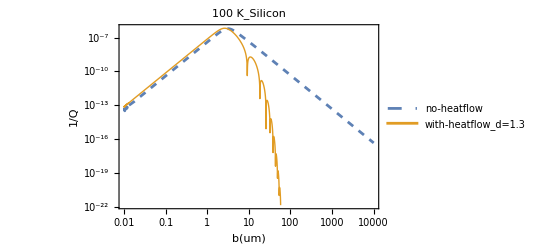

```mathematica
QNob100 =Abs[ ΔE(6/(2ξ)^2-6/(2ξ)^3(Sinh[2ξ]+Sin[2ξ])/(Cosh[2ξ]+Cos[2ξ]) )]/.
{ξ->an/(4 3^(1/4))b^(3/2)/(L √lT)}/.
{d->1.3,lT->2.017 10^-1,an->4.73,ΔE->1.232 10^-6,L->10};

QNob100g=LogLogPlot[{QNob100,Qb100},{b,0.01,10000},PlotLabel->100K_Silicon, PlotStyle->{Dashed,Thick},PlotLegends->Placed[{"no-heatflow","with-heatflow_d=1.3"},{0.3,0.25}], Frame->True,FrameLabel->{b[um],Q^-1}]
```

10K

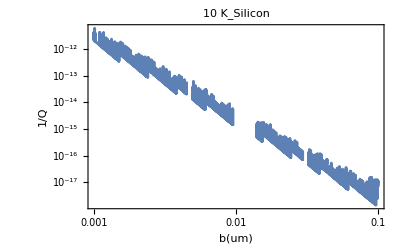

```mathematica
Qb10=Abs[3/(4 ξ^3)-ΔE/(Cos[2 d ξ]+Cosh[2 d ξ])(Cos[ξ(d-1)]Sinh[ξ(d+1)]+Cos[ξ(d+1)]Sinh[ξ(1-d)]-Sin[ξ(d-1)]Cosh[ξ(1+d)]+Sin[ξ(1+d)]Cosh[ξ(1-d)]-2ξ(Cos[ξ(d-1)]Cosh[ξ(1+d)]+Cos[ξ(d+1)]Cosh[ξ(1-d)]))]/.
{ξ->an/(4 3^(1/4))b^(3/2)/(L √lT)}/.
{d->1.3,lT->4.977 10^2,an->4.73,ΔE->2.319 10^-10,L->10};
Qb10g=LogLogPlot[Qb10,{b,0.001,0.1},PlotLabel->10K_Silicon, Frame->True,FrameLabel->{b[um],Q^-1}]
```

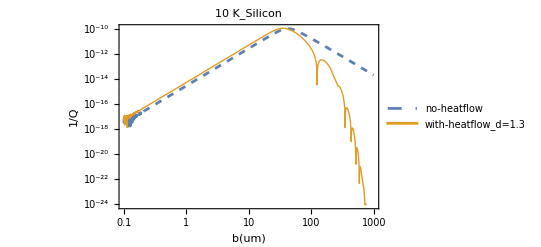

```mathematica
QNob10 =Abs[ ΔE(6/(2ξ)^2-6/(2ξ)^3(Sinh[2ξ]+Sin[2ξ])/(Cosh[2ξ]+Cos[2ξ]) )]/.
{ξ->an/(4 3^(1/4))b^(3/2)/(L √lT)}/.
{d->1.3,lT->4.977 10^2,an->4.73,ΔE->2.319 10^-10,L->10};
QNob10g=LogLogPlot[{QNob10,Qb10},{b,0.1,1000},PlotLabel->10K_Silicon, PlotStyle->{Dashed,Thick},PlotLegends->Placed[{"no-heatflow","with-heatflow_d=1.3"},{0.3,0.25}], Frame->True,FrameLabel->{b[um],Q^-1}]
```

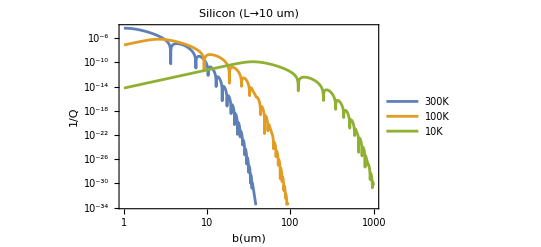

```mathematica
LogLogPlot[{Qb300,Qb100,Qb10},{b,1,1000},PlotLabel-> Silicon ( L->10um), Frame->True,PlotLegends->Placed[{"300K","100K","10K"},{0.3,0.2}],FrameLabel->{b[um],Q^-1}]
```

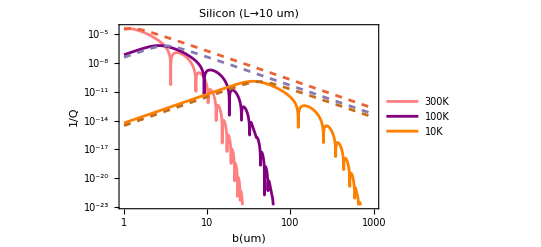

```mathematica
LogLogPlot[{Qb300,Qb100,Qb10,QNob300,QNob100,QNob10},{b,1,1000},PlotLabel-> Silicon ( L->10um),PlotStyle->{Pink,Purple,Orange,Dashed,Dashed,Dashed}, Frame->True,PlotLegends->Placed[{"300K","100K","10K"},{0.2,0.2}],FrameLabel->{b[um],Q^-1}]
```